```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching ""Global`*"".

```mathematica
h={{-Δ/2,g},{g,Δ/2}}
```

{{-Δ/2,g},{g,Δ/2}}

```mathematica
ev=Eigenvalues[h]
```

{-1/2 √(4 g^2+Δ^2),1/2 √(4 g^2+Δ^2)}

```mathematica
frequency = ev[[2]]-ev[[1]]
```

√(4 g^2+Δ^2)

```mathematica
Series[ev[[2]],{Δ,0,2}]
```

√(g^2)+(√(g^2) Δ^2)/(8 g^2)+O[Δ]^3

```mathematica
evs=Map[FullSimplify[#/Norm[#]]&,Eigenvectors[h]]
```

{{(-Δ-√(4 g^2+Δ^2))/(g √(4+Abs[(Δ+√(4 g^2+Δ^2))/g]^2)),2/(√(4+Abs[(Δ+√(4 g^2+Δ^2))/g]^2))},{(-Δ+√(4 g^2+Δ^2))/(g √(4+Abs[(Δ-√(4 g^2+Δ^2))/g]^2)),2/(√(4+Abs[(Δ-√(4 g^2+Δ^2))/g]^2))}}

```mathematica
evs1=FullSimplify[Assuming[g>0,Assuming[Δ>0,FullSimplify[evs[[1]]/Norm[evs[[1]]]]]]]
```

{-(Δ+√(4 g^2+Δ^2))/(g √(8+(2 Δ (Δ+√(4 g^2+Δ^2)))/g^2)),2/(√(8+(2 Δ (Δ+√(4 g^2+Δ^2)))/g^2))}

```mathematica
evs2=FullSimplify[Assuming[g>0,Assuming[Δ>0,FullSimplify[evs[[2]]/Norm[evs[[2]]]]]]]
```

{(-Δ+√(4 g^2+Δ^2))/(g √(8+(2 Δ (Δ-√(4 g^2+Δ^2)))/g^2)),(√(1+Δ/(√(4 g^2+Δ^2))))/(√2)}

```mathematica
FullSimplify[FullSimplify[Dot[evs1,evs2]]]
```

(-1+√(1/(1+Δ/(√(4 g^2+Δ^2)))) √(1+Δ/(√(4 g^2+Δ^2))))/(2 √(1/(1-Δ/(√(4 g^2+Δ^2)))) √(1/(1+Δ/(√(4 g^2+Δ^2)))))

```mathematica
FullSimplify[Dot[evs[[1]],evs[[2]]] ]
```

0

```mathematica
amplitude = Abs[Assuming[g>0,Assuming[Δ>0,FullSimplify[evs1[[1]]*evs2[[1]]-evs1[[2]]*evs2[[2]]]]]]
```

2 Abs[g/(√(4 g^2+Δ^2))]

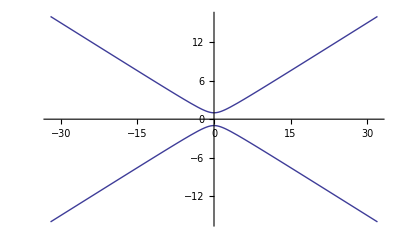

```mathematica
Plot[{ev[[1]],ev[[2]]} /.{g->1},{Δ,-32,32}]
```

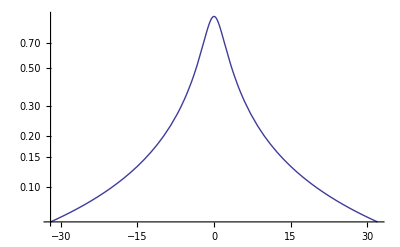

```mathematica
LogPlot[{amplitude} /. {g->1},{Δ,-32,32},PlotRange->Full]
```

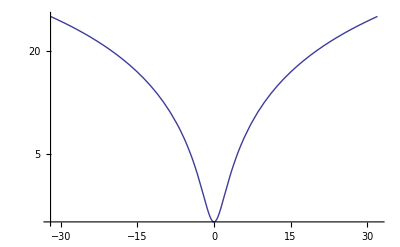

```mathematica
LogPlot[{frequency} /. {g->1},{Δ,-32,32},PlotRange->Full]
```

```mathematica
Export[NotebookDirectory[]<>"swap_energies.csv",Map[Block[{Δ=#},{#,ev[[1]],ev[[2]]} /. {g->1}]&,Range[-60,60,0.01]] ]
```

E:\cygwin\home\adewes\thesis\material\mathematica\swap_energies.csv

```mathematica
Export[NotebookDirectory[]<>"swap_amplitude.csv",Map[Block[{Δ=#},{#,amplitude} /. {g->1}]&,Range[-60,60,0.01]] ]
```

E:\cygwin\home\adewes\thesis\material\mathematica\swap_amplitude.csv

```mathematica
Export[NotebookDirectory[]<>"swap_frequency.csv",Map[Block[{Δ=#},{#,frequency} /. {g->1}]&,Range[-60,60,0.01]] ]
```

E:\cygwin\home\adewes\thesis\material\mathematica\swap_frequency.csv

```mathematica
Solve [Abs[amplitude] == 0.05,{Δ}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Δ→-39.95 g},{Δ→39.95 g}}